# Spencer Lyon

## Physics 321

Homework Due 9-21-12

## P6.10

This is just a simple conservation of energy equation.

The mass is released from rest so initial kinetic energy is 0. When the mass is released and the cord has returned to its normal position its potential energy due to the cord is zero so the conservation of energy equation reduces to:

V_0 = T_1

Below is a diagram of the system when the mass is pulling the cord back

From the geometry shown in my figure, we can see that if we look only at one half of the cord, we it will have been streteched from 𝒶 to 5/4 a. This means there is a total extension of 1/4 a in each half.

From example 6.14, we get the equation for the potential energy stored in a cord as:

V = 1/2 α a^2,

where α is the strengh of the cord, and a is the extension of the cord away from its equilibrium length.

We also need to know the relative strength of each 1/2 of the cord. Using Hooke’s law (F = k x) and assuming the force needs to be constant, we can see that if x is 1/2 its normal value then k needs to be twice its normal value. Applying this analogy to our problem gives is that the strength of each 1/2 of the cord is equal to 2α. Using this and equation (0.2) we get the following expression for the potential energy in each 1/2 of the cord:

V = 1/2(2α) (1/4 a)^2 = 1/16 α a^2

To get the potential energy in the entire cord we simple double that value to get V_0 = 1/8 α a^2

Now we use the general equaiton for kinetic energy (T = 1/2 m v^2) and use equation (0.1) to get the final answer:

1/8 α a^2 = 1/2 m v^2 → 1/4(α a^2)/m = v^2 → v = √(1/4(α a^2)/m)□

## P6.16

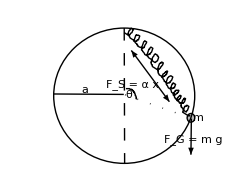

If we look at the triangle created two legs of length a and the spring we can solve for the length spring in terms of theta and a. This is a SAS (side-angle-side) representation, so the length of the spring at any time is given by following the law of cosines. In specific, the length will be equal to:

l = a^2 + a^2 - 2 (a)(a)cos(θ) = 2a^2(1 - cos θ)

With that in mind and using equation (0.2) from above, the potential energy of the spring is equal to

V_s = 1/2 α (2a^2(1 - cos θ) - 3/2 a)^2

From the equation listed as F_G we can get that the graviatational potential energy is equal to -𝓂 ℊ 𝒶 cos (180 - θ). This makes the total potential energy of the system equal to the following.

V = V_s +V_G =1/2 α (2a^2(1 - cos θ) - 3/2 a)^2 -  m g a cos (180 - θ)

To find an equililbirum position, we simply need to see at which angles we have a non-chaning potential energy. We will just take the derivative and set it equal to 0. Mathematica can do this for us:

```mathematica
Vprime = D[1/2 α * (2 a(1 - Cos[θ]) - 3/2 a)^2 - m g a Cos[π - θ], θ]
Vprime2 = D[1/2 α * (2 a(1 - Cos[θ]) - 3/2 a)^2 - m g a Cos[π - θ], {θ, 2}]
```

2 a α sin(θ) (2 a (1-cos(θ))-(3 a)/2)-a g m sin(θ)

1/2 α (8 a^2 sin^2(θ)+4 a cos(θ) (2 a (1-cos(θ))-(3 a)/2))-a g m cos(θ)

We will plug θ = π rad = 180 ° into the Vprime equation to make sure the bottom is an equilibirum position:

```mathematica
Vprime/.θ-> π
```

0

As we can see, θ = 180° is an equilibrium position. We will now check stability by looking at V’’(π) and see what the 2nd derivative is. We will also solve V’’(π) = 0 for α.

```mathematica
(Vprime2/. θ -> π)//FullSimplify
alpha = α/. Solve[(Vprime2 /. θ -> π) ==0 , α][[1]]
```

a g m-(a^2 α)/4

(4 g m)/a

Stability happens when V’’ < 0  so as long as α is less than (g m)/(5 a)we will get stability.

Case 1 is when α = 2 m g / a. Case two is when α = 5 m g a. We will test to see if these are greater than or less than the value of α we solved for above.

(4 g m)/a>(2 g m)/a→ 2 > 1.

The above is true and therefore  case1 (when α = 2 m g / a) is a stable equilibrium.

(4 g m)/a>(5 m g)/a → 4 > 5

The above is not true and therefore  case 2 (when α = 5 m g / a) is an unstable equilibrium.